Aplicación repetida de funciones

f[x] aplica f a x. f[f[x]] aplica f a f[x]; de hecho, anida la aplicación de f. Es usual que se quiera repetir o anidar una función.

Aquí se forma una lista con los resultados de anidar f 4 veces:

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

Si la función que se usa es Framed, resulta un poco más obvio lo que está sucediendo:

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

Cuando se quiere ver la lista de los resultados de anidaciones sucesivas, se usa NestList. Si solo interesa el resultado final, se usa Nest.

Aquí aparece el resultado final de 5 niveles de anidación:

```mathematica
Nest[Framed,x,5]
```

x

Aplique EdgeDetect de manera anidada a una imagen encontrando: primero, bordes, luego bordes de los bordes, y así sucesivamente.

Detecte en una imagen bordes, de manera anidada:

```mathematica
NestList[EdgeDetect,-Graphics-,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use una función pura para detectar, en cada paso, los bordes y al mismo tiempo dar el negativo de color:

```mathematica
NestList[ColorNegate[EdgeDetect[#]]&,-Graphics-,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Comenzando con el rojo, mezcle con amarillo de manera anidada, a modo de obtener cada vez más amarillo.

Añada a la mezcla otro amarillo en cada paso:

```mathematica
NestList[Blend[{#,Yellow}]&,Red,20]
```

{RGBColor[1, 0, 0],RGBColor[1, Rational[1, 2], 0],RGBColor[1, Rational[3, 4], 0],RGBColor[1, Rational[7, 8], 0],RGBColor[1, Rational[15, 16], 0],RGBColor[1, Rational[31, 32], 0],RGBColor[1, Rational[63, 64], 0],RGBColor[1, Rational[127, 128], 0],RGBColor[1, Rational[255, 256], 0],RGBColor[1, Rational[511, 512], 0],RGBColor[1, Rational[1023, 1024], 0],RGBColor[1, Rational[2047, 2048], 0],RGBColor[1, Rational[4095, 4096], 0],RGBColor[1, Rational[8191, 8192], 0],RGBColor[1, Rational[16383, 16384], 0],RGBColor[1, Rational[32767, 32768], 0],RGBColor[1, Rational[65535, 65536], 0],RGBColor[1, Rational[131071, 131072], 0],RGBColor[1, Rational[262143, 262144], 0],RGBColor[1, Rational[524287, 524288], 0],RGBColor[1, Rational[1048575, 1048576], 0]}

Si se aplica sucesivamente una función que suma 1, se obtienen enteros sucesivos.

Sume 1 de manera anidada, para obtener números sucesivos:

```mathematica
NestList[#+1&, 1, 15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

Multiplique por 2 de manera anidada, para obtener potencias de 2.

El resultado se duplica cada vez, dando una lista de las potencias de 2:

```mathematica
NestList[2*#&,1,15]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

Si se eleva al cuadrado de manera anidada, se alcanzan números grandes muy rápidamente:

```mathematica
NestList[#^2&,2,6]
```

{2,4,16,256,65536,4294967296,18446744073709551616}

También se pueden anidar las raíces cuadradas.

Aplique la raíz cuadrada de manera anidada:

```mathematica
NestList[Sqrt[1+#]&,1,5]
```

{1,√2,√(1+√2),√(1+√(1+√2)),√(1+√(1+√(1+√2))),√(1+√(1+√(1+√(1+√2))))}

La versión decimal del resultado converge rápidamente (a la razón áurea):

```mathematica
NestList[Sqrt[1+#]&,1,10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

RandomChoice elige al azar de una lista. Esto puede usarse, por ejemplo, para crear una función pura que sume al azar +1 o −1.

En cada paso, sume o reste 1, al azar, comenzando de 0:

```mathematica
NestList[#+RandomChoice[{+1,-1}]&,0,20]
```

{0,1,0,-1,-2,-3,-4,-5,-6,-5,-6,-5,-4,-5,-4,-3,-4,-3,-2,-1,-2}

Aquí se generan 500 pasos de una “caminata aleatoria”:

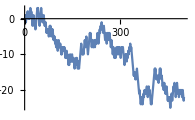

```mathematica
ListLinePlot[NestList[#+RandomChoice[{+1,-1}]&,0,500]]
```

Hasta ahora se ha usado NestList iterativamente, de hecho, para efectuar una cadena de aplicaciones de una función dada. Ahora bien, también puede usarse para fines de recursión, donde lo que se anida es el patrón mismo de aplicaciones de la función.

Aquí se efectúa una cadena de aplicaciones de la función f:

```mathematica
NestList[f[#]&,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

Aquí el patrón de aplicaciones de f es más complicado:

```mathematica
NestList[f[#,#]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

Si se enmarcan los resultados se podrá entender mejor lo que está sucediendo:

```mathematica
NestList[Framed[f[#,#]]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

Si se acomoda todo en columnas, se deja ver el patrón anidado de aplicaciones de la función.

En cada nivel, las cajas anidadas se combinan en pares, de manera recursiva:

```mathematica
NestList[Framed[Column[{#,#}]]&,x,3]
```

{x,x
x,x
x
x
x,x
x
x
x
x
x
x
x}

A continuación, una secuencia de rejillas anidadas de manera recursiva:

```mathematica
NestList[Framed[Grid[{{#,#},{#,#}}]]&,x,3]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

Aquí se forma el comienzo de una estructura fractal:

```mathematica
NestList[Framed[Grid[{{0,#},{#,#}}]]&,x,3]
```

{x,0 | x
x | x,0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x,0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x}

Pueden obtenerse sin dificultad estructuras de tipo recursivo muy vistosas:

```mathematica
NestList[Flatten[{#,Rotate[#,90°],Rotate[#,270°]}]&,"R",4]
```

{R,{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}}}}

No todos los resultados de una recursión son tan complicados. He aquí un ejemplo donde se suman sucesivamente dos copias desplazadas de una lista, como en {0,1,2,1}+{1,2,1,0}.

Añada, al principio y al final, un 0 a una lista y, luego, sume los resultados:

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},5]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1}}

Si el resultado se acomoda en una rejilla, se va formando el triángulo de Pascal de los coeficientes binomiales:

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1

Aquí se muestra otro ejemplo de recursión con NestList.

Forme una estructura recursiva con dos funciones, f y g:

```mathematica
NestList[{f[#],g[#]}&,x,3]
```

{x,{f[x],g[x]},{f[{f[x],g[x]}],g[{f[x],g[x]}]},{f[{f[{f[x],g[x]}],g[{f[x],g[x]}]}],g[{f[{f[x],g[x]}],g[{f[x],g[x]}]}]}}

Es bastante complicado entender la estructura así formada, aun si se acomodan las cosas en columnas.

Acomodar en columnas la estructura recursiva:

```mathematica
NestList[Column[{f[#],g[#]}]&,x,3]
```

{x,f[x]
g[x],f[f[x]
g[x]]
g[f[x]
g[x]],f[f[f[x]
g[x]]
g[f[x]
g[x]]]
g[f[f[x]
g[x]]
g[f[x]
g[x]]]}

NestGraph es básicamente como NestList, salvo que produce un grafo en vez de una lista. Aplica una función repetidamente para determinar con cuáles nodos debe conectarse un nodo particular. En este caso se produce un árbol de nodos, lo que deja más claro qué está sucediendo.

Comenzando con x, se va conectando repetidamente con la lista de nodos obtenidos al aplicar la función:

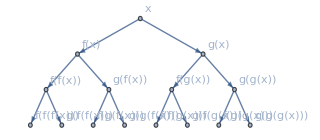

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->All]
```

Aplicar repetidamente una función numérica para formar otra estructura de árbol:

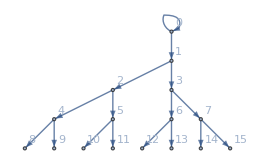

```mathematica
NestGraph[{2#,2#+1}&,0,4,VertexLabels->All]
```

Se puede usar NestGraph para “reptar” hacia afuera, creando una red. Como ejemplo, podría aplicarse repetidamente una función tal que, para cada país, produjera la lista de sus países colindantes. El resultado sería una red que conecta los países colindantes; así, podría comenzarse con Suiza.

“Reptar” hacia afuera 2 pasos a partir de Suiza, conectando cada país con los que le son colindantes:

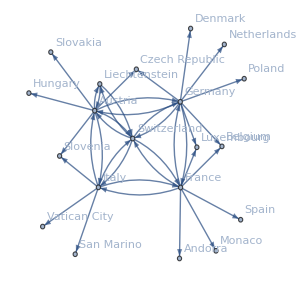

```mathematica
NestGraph[#["BorderingCountries"]&,LinguisticAssistant,2,VertexLabels->All]
```

Un ejemplo más: comenzando con la palabra “hello”, conecte sucesivamente cada palabra con otras 3 de la lista de palabras comunes que Nearest considere más cercanas a ella.

Cree una red de palabras cercanas con respecto a cambios de una letra:

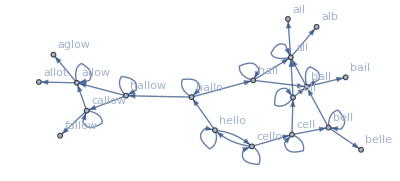

```mathematica
NestGraph[Nearest[WordList[ ],#,3]&,"hello",4,VertexLabels->All]
```

Vocabulario

NestList[f,x,n] |   | construye la lista que resulte de aplicar f a x hasta n veces
Nest[f,x,n] |   | obtiene el resultado de aplicar f a x exactamente n veces 
NestGraph[f,x,n] |   | forma un grafo aplicando f con anidación, a partir de x

"11 Exercises Available"
"with 5 extras" | "Get Started »"

Construya una lista con los resultados de anidar Blur hasta 10 veces, comenzando con una “X” rasterizada de tamaño 30. »

| Expected output: |  
  | {,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Comenzando con x, forme una lista anidando Framed hasta 10 veces, con un trasfondo de color aleatorio en cada ocasión. »

| Sample expected output: |  
  | {x,x,x,x,x,x,x,x,x,x,x} |

A partir de una “A” de tamaño 50, construya una lista poniendo 5 veces un marco y dando una rotación aleatoria de manera anidada. »

| Sample expected output: |  
  | {"A","A","A","A","A","A"} |

Obtenga un gráfico con los puntos unidos de 100 iteraciones del mapeo logístico 4 #(1-#)&, comenzando en 0.2. »

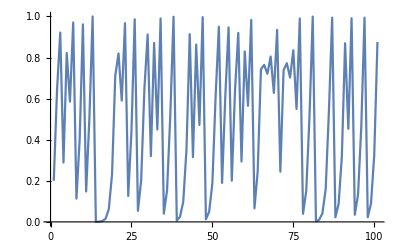
| Expected output: |  
  | -Graphics- |

Encuentre el valor numérico del resultado de 30 iteraciones de 1+1/#& comenzando con 1. »

| Expected output: |  
  | 1.61803 |

Cree la lista de las 10 primeras potencias de 3 (comenzando en 0), usando multiplicación anidada. »

| Expected output: |  
  | {1,3,9,27,81,243,729,2187,6561,19683,59049} |

Forme una lista con los resultados de anidar la función (#+2/#)/2& (el método de Newton) hasta 5 veces, comenzando con 1.0, y restando √2a cada uno de los resultados. »

| Expected output: |  
  | {-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16} |

Obtenga el gráfico, en 2D, de una caminata aleatoria de 1 000 pasos, comenzando en {0,0} donde, en cada paso, se añade a las coordenadas una pareja de números aleatorios entre −1 y +1. »

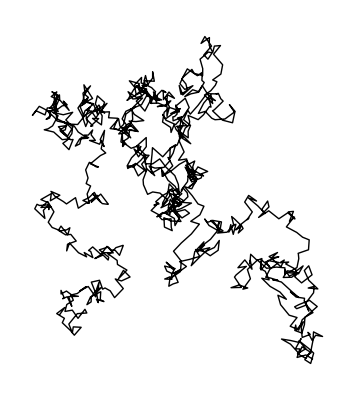
| Sample expected output: |  
  | -Graphics- |

Obtenga un gráfico de arreglo de 50 pasos del triángulo de Pascal módulo 2, comenzando con {1} y uniendo, de manera anidada, {0} al principio y al final, y sumando estos resultados módulo 2. »

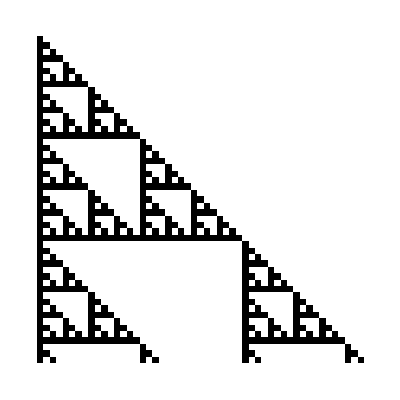
| Expected output: |  
  | -Graphics- |

Genere un grafo comenzando de 0, y luego conectando de manera anidada 10 veces cada nodo de valor n con los de valor n+1 y 2n. »

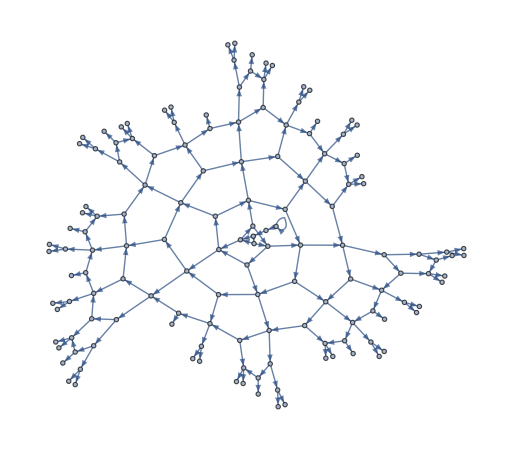
| Expected output: |  
  | -Graphics- |

Genere un grafo, encontrando de manera anidada los países colindantes, comenzando con Estados Unidos, durante 4 iteraciones. »

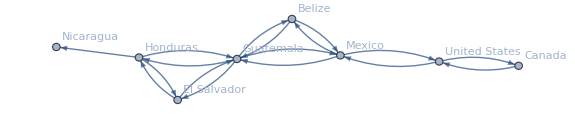
| Expected output: |  
  | -Graphics- |

Produzca un gráfico con los puntos unidos de 100 iteraciones de la función congruencia lineal Mod[59#,101]&, comenzando con 1. »

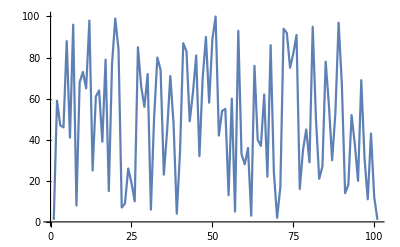
| Expected output: |  
  | -Graphics- |

Cree la lista de 5 torres de potencias de 2, es decir, 2^2^2...^2 n veces, con n de 0 a 4. »

| Expected output: |  
  | {1,2,4,16,65536} |

Cree la lista de 20 torres de potencias de 1.2, es decir,1.2^1.2^...^1.2 n veces, con n de 0 a 19. »

| Expected output: |  
  | {1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773} |

Genere la lista de los valores numéricos obtenidos en hasta 10 anidaciones de la función Sqrt[1+#]&. »

| Expected output: |  
  | {1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803} |

Produzca el gráfico 3D, de una caminata aleatoria de 1000 pasos, comenzando en {0,0,0} donde, en cada paso, se añade a las coordenadas una terna de números aleatorios entre −1 y +1. »

| Expected output: |  
  | -Graphics3D- |

Preguntas y respuestas

¿Cuál es la diferencia entre iteración y recursión?

Si se ejecuta algo repetidamente, se está haciendo una iteración. Si se toma el resultado de una operación y se le aplica la misma operación, se trata de una recursión. Se presta un poco a confusión, porque los casos simples de recursión son de iteración. NestList siempre efectúa la recursión, pero si aparece solamente una ranura en la función, la recursión puede “desenrollarse” para convertirse en una iteración.

¿Qué relación hay entre anidación, recursión y fractales?

Están estrechamente relacionados. No hay definiciones precisas, pero los fractales son básicamente formas geométricas que exhiben algún tipo de estructura recursiva.

¿Qué es el triángulo de Pascal?

Se trata de una estructura muy común que se describe en las matemáticas elementales. Su definición es muy cercana al código en Wolfram Language que se ha visto aquí: en cada fila, cada número se calcula como la suma de los dos números directamente arriba de él, al lado izquierdo y al derecho. Cada fila contiene los coeficientes del desarrollo de (1+x)^n.

¿Es NestGraph como un rastreador web?

Conceptualmente, lo es. Se puede concebir como el análogo de comenzar en una página web y visitar, a partir de ahí, todos los vínculos que tiene, y continuar así, recursivamente, con el proceso. Se verá un ejemplo de esto en la Sección 44.

¿Cómo es que algunos de los países, pero no todos, tienen flechas bidireccionales en el grafo de países colindantes?

Si se ejecutara NestGraph en un número suficiente de pasos, todos los países tendrían flechas bidireccionales; ya que, si A colinda con B, entonces B colinda con A. Pero el proceso se detuvo después del segundo paso, así que no se alcanzó a llegar a muchas de las conexiones inversas.

¿Por qué se usa NestList en algo como NestList[2*#&,1,15]?

No es necesario. Se puede simplemente usar Power, como en Table[2^n,{n,0,15}]. Pero vale la pena ver cómo surge la secuencia Plus, Times, Power del anidamiento sucesivo(p.ej., NestList[2+#&,0,15] es Table[2*n,{n,0,15}]).

¿Existe alguna forma de detener la aplicación de una función cuando ya no hay cambios en los resultados?

Sí. Se utiliza para ello FixedPoint o FixedPointList (ver la Sección 41).

Nota técnica

El ejemplo sobre palabras cercanas puede ser mucho más eficiente calculando, primero, una NearestFunction, y luego usándola repetidamente; mejor que calcular Nearest desde cero para cada palabra. Este ejemplo está estrechamente relacionado con NearestNeighborGraph, que se verá en la Sección 22.

Para explorar más

Guía para la iteración funcional en Wolfram Language »